# RUST from Mathematica

## Setup

Set your environment variables below

```mathematica
LTDFolder = "/Users/zeno/Desktop/LTD/program/pynloop";
PythonInterpreter = "/usr/local/bin/python3";
CUBAPath = "/Users/zeno/Desktop/LTD/program/pynloop/rust_backend";
TopologyName ="Box_5E";
```

Then start the process hook to the Python bindings

We can verify that it is indeed running and waiting to be fed with data

We can now build a function using the hook to access the deformation

```mathematica
GetDeformationFromRust[hook_, RealMomenta_]:=Module[
{RawOutput, DeformedMomenta},

(* Write the real momenta to sys.stdin of the hook *)
WriteLine[hook,
StringJoin[
Riffle[Table[
StringJoin[
Riffle[
Table[ToString[NumberForm[ke,Infinity,ExponentFunction->(Null&)]],{ke, k}],
" "]
],
{k,RealMomenta}
]," "]
]
];

(* Now recover the deformed momenta *)
RawOutput = ReadLine[hook];
(*Print[RawOutput];*)
(* Parse it *)
(*DeformedMomenta = Table[Read[StringToStream[ke],Number],{ke,StringSplit[RawOutput]}];*)

DeformedMomenta = Table[
Read[
If[ke=="nan",
Print["NaN from:"<>ToString[RealMomenta]];
StringToStream["0"],
StringToStream[ke]],
Number],{ke,StringSplit[RawOutput]}];

(* Reshape and return *)
ArrayReshape[DeformedMomenta,{Length[DeformedMomenta]/4,4}]
]
```

## Test it now!

### Run the LTD Hook

```mathematica
LTDHook = StartProcess[{
PythonInterpreter,
LTDFolder<>"/"<>"get_deformation.py",
TopologyName},
ProcessEnvironment-><|"DYLD_LIBRARY_PATH"->CUBAPath|>
];

ProcessStatus[LTDHook]
```

Running

### Function providing the deformed momenta

```mathematica
getMomenta[kx_?NumberQ, ky_?NumberQ, kz_?NumberQ,lx_?NumberQ, ly_?NumberQ, lz_?NumberQ]:=Module[{myvectot},
myvectot=GetDeformationFromRust[LTDHook,
  {{kx,ky,kz},{lx,ly,lz}}];
tscaling=myvectot[[3]][[2]];
defvec={myvectot[[2]][[2]],myvectot[[2]][[3]],myvectot[[2]][[4]]};
{{tscaling*kx,tscaling*ky,tscaling*kz}-I*defvec,{tscaling*lx,tscaling*ly,tscaling*lz}}
]
```

```mathematica
getMomenta[1,2,3,2,3,4][[1]]
```

{0.133631-0.167567 ⅈ,0.267261-0.251351 ⅈ,0.400892-0.335135 ⅈ}

### Definition of pinched surface

```mathematica
pinchedSurface[{kx_?NumberQ, ky_?NumberQ, kz_?NumberQ},{lx_?NumberQ, ly_?NumberQ, lz_?NumberQ}]:=Sqrt[kx^2+ky^2+kz^2]+Sqrt[(kx-lx)^2+(ky-ly)^2+(kz-lz)^2]-Sqrt[lx^2+ly^2+lz^2+1]
```

Try it!

```mathematica
pinchedSurface[getMomenta[1,2,3,2,3,4][[1]],getMomenta[1,2,3,2,3,4][[2]]]
```

-0.508708-0.00144289 ⅈ

1

0.

### Contour Plots

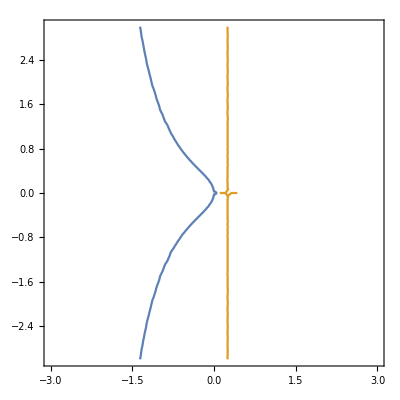

```mathematica
cp1=ContourPlot[{Re[pinchedSurface[getMomenta[x,y,0.,0.5,0.,0.][[1]],getMomenta[x,y,0,0.5,0.,0][[2]]]]==0.,Im[pinchedSurface[getMomenta[x,y,0.,0.5,0.,0.][[1]],getMomenta[x,y,0,0.5,0.,0][[2]]]]==0.},{x,-3,3},{y,-3,3}]
```

### Examples (nothing interesting here, stuff I used to learn about the code)

```mathematica
GetDeformationFromRust[LTDHook,
  {{1.5,0.,0.},{0.,0.1,0.300001}}
  ]
```

{{4.00029,0.,0.0666667,0.200001},{0.010829,0.,0.0649786,0.194937},{-0.666667,0.333333,0.666667,0.333333}}

```mathematica
ProcessStatus[LTDHook]
```

Running

```mathematica
ClearAll[vec]
```

```mathematica
vec[delta_?NumberQ]:=Block[{},
(*Print[delta];*)
GetDeformationFromRust[LTDHook,
 {{0.1,0.3,0.3},{0.1,0.3,0.3+delta(*Exp[-delta]*)}} ]
]
```

```mathematica
vec[0.1]
```

{{0.,0.229416,0.688247,0.917663},{0.,0.0438529,0.131559,0.175412}}

```mathematica
vec1[delta_?NumberQ]:=Block[{myvec},
myvec=vec[delta];
Sqrt[myvec[[2]][[2]]^2+myvec[[2]][[3]]^2+myvec[[2]][[4]]^2]
]
```

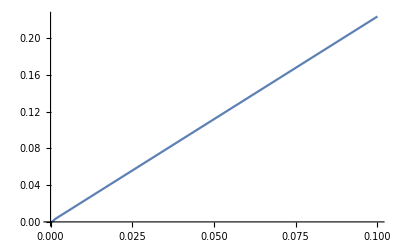

```mathematica
Plot[
vec1[delta],
{delta,0.,0.1}]
```

```mathematica
defvec[delta_?NumberQ]:=Block[{myvec},
myvec=vec[delta];
Re[Sqrt[(myvec[[1]][[2]]-I*myvec[[2]][[2]])^2+(myvec[[1]][[3]]-I*myvec[[2]][[3]])^2+(myvec[[1]][[4]]-I*myvec[[2]][[4]])^2]]
]
```

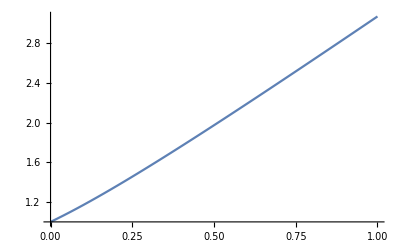

```mathematica
Plot[
defvec[delta],
{delta,0.,1}]
```

```mathematica
vec2d[delta_?NumberQ,gamma_?NumberQ]:=Block[{},
(*Print[delta];*)
GetDeformationFromRust[LTDHook,
 {{0.1,0.3,0.3},0.5*{0.1,0.3+gamma,0.3+delta(*Exp[-delta]*)}} ]
]
```

```mathematica
defvec2d[delta_?NumberQ,gamma_?NumberQ]:=Block[{myvec},
myvec=vec2d[delta,gamma];
Re[Sqrt[(myvec[[1]][[2]]-I*myvec[[2]][[2]])^2+(myvec[[1]][[3]]-I*myvec[[2]][[3]])^2+(myvec[[1]][[4]]-I*myvec[[2]][[4]])^2]]
]

defvec2dnorm[delta_?NumberQ,gamma_?NumberQ]:=Block[{myvec},
myvec=vec2d[delta,gamma];
Re[Sqrt[(myvec[[2]][[2]])^2+(myvec[[2]][[3]])^2+(myvec[[2]][[4]])^2]]
]

defvec2d[0.00001,0.00002]
defvec2dnorm[0.00001,0.00002]
```

0.500024

7.44505×10^-16

```mathematica
ContourPlot[
defvec2d[delta,gamma]==0,
{delta,-0.5,0.5},{gamma,-0.5,0.5}]
```

-Graphics-